```mathematica
Needs["Screening`",NotebookDirectory[]<>"../packages/Screening.wl"]
Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
```

#### Earth parameters

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

```mathematica
FeNucCoeffs
SiNucCoeffs
MgNucCoeffs
ONucCoeffs
```

<|a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26,nI→1.402×10^29,β→1.32379×10^19|>

<|a→{6.2915,3.0353,1.9891,1.541},b→{2.4386,32.3337,0.6785,81.6937},c→1.1407,Z→13.9976,A→28,rn→3.46171×10^-15,mN→4.648×10^-26,nI→4.995×10^28,β→2.76063×10^19|>

<|a→{5.4204,2.1735,1.2269,2.3073},b→{2.8275,79.2611,0.38,7.1937},c→0.8584,Z→11.9865,A→24,rn→3.28833×10^-15,mN→3.984×10^-26,nI→4.362×10^28,β→2.76063×10^19|>

<|a→{3.0485,2.2868,1.5463,0.867},b→{13.2771,5.7011,0.3239,32.9089},c→0.2508,Z→7.9994,A→16,rn→2.87262×10^-15,mN→2.656×10^-26,nI→1.435×10^29,β→2.76063×10^19|>

### Run

#### par card

```mathematica
NuccoeffList={FeNucCoeffs,SiNucCoeffs,MgNucCoeffs,ONucCoeffs};
```

```mathematica
{meDrats ,v0}= {{1.0 10^-4,1.0 10^-3,1.0 10^-2}[[1;;1]],20.0 10^3};
parcard = Table[Table[Table[<|"κ"->10^κ,"mpD"->("JpereV")/("c")^2 10^mpd,"meD"->meDrats[[meDs]]("JpereV")/("c")^2 10^mpd,"v0"->v0,"βD"->Capture`v0toβD[v0,meDrats[[meDs]]("JpereV")/("c")^2 10^mpd,("JpereV")/("c")^2 10^mpd]["βD"]|>//Simplify,{κ,-14,-7,1}],{mpd,6,15,1}]/.SIConstRepl,{meDs, Length[meDrats]}];
δs = {10^-5,10^-3,10^-2,10^-1,0.35,0.65,1,1.5};
δScanLists = Table[Table[<|"δ"->δs[[i]],"pdict"->parcard[[meDs]]|>,{i,Length[δs]}],{meDs,Length[meDrats]}];
```

```mathematica
{fDs,αDbyαs}={{0.01,0.05}[[1;;1]],{1,0.1}[[2;;2]]};
```

#### run

run a little sun here and a lot of sun in other kernel

```mathematica
Monitor[Do[ScanOverUnfixedParameters[δScanLists[[meD]],NuccoeffList,αDbyαs,fDs,{"vescSpD"->1/(√2)43 10^3,"vescSeD"->1/(√2)43 10^3}],{meD,Length[meDrats]}(*,{fD,Length[fDs]},{αDbyα,Length[αDbyαs]}*)],{meD}]
```

Running: {1,0.1,0.01}

Finished running the PDicts for: 
{v0,meD/mpD}={v0,meD/mpD}/.pdict

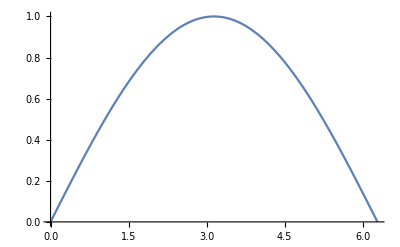

```mathematica
Plot[Sin[x/2],{x,0,2π}]
```